```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v2

### Lattice

```mathematica
HotQCDp=Flatten[Import["../../../LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../../../LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../../../LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../../../LQCDdata/hotdpt4u.dat"]];
Tcl=1;
Hotpdown=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["../../../LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["../../../LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["../../../LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT/Tcl,WBp-WBdp}];
WBup=Transpose[{WBT/Tcl,WBp+WBdp}];
WBcs=Table[Import["../../../LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["../../../LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT/Tcl,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT/Tcl,WBcs-WBcserr}];
WBp2025=Flatten[Import["../../../LQCDdata/WB2025/PT4WB.dat"]];
WBdp2025=Flatten[Import["../../../LQCDdata/WB2025/PT4WB_erro.dat"]];
WBT2025=Flatten[Import["../../../LQCDdata/WB2025/TWB.dat"]];
WBdown2025=Transpose[{WBT2025/Tcl,WBp2025-WBdp2025}];
WBup2025=Transpose[{WBT2025/Tcl,WBp2025+WBdp2025}];
```

### Model

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,500,550};
T=Table[i,{i,21,300}];
poT4data=Table[(Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/chi0.dat"]]-Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/chi0.dat"]][[1]])/T^4,{i,1,Length[mub]}];
c2data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/c2.dat"]],{i,1,Length[mub]}];
c3data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/c3.dat"]],{i,1,Length[mub]}];
c4data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/c4.dat"]],{i,1,Length[mub]}];
c5data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/c5.dat"]],{i,1,Length[mub]}];
c6data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/c6.dat"]],{i,1,Length[mub]}];
```

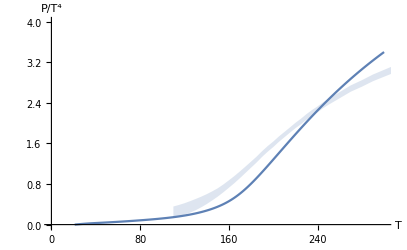

```mathematica
PlotP=Show[ListLinePlot[{Transpose[{T,poT4data[[1]]}](*,Hotpdown,Hotpup,Transpose[{T,poT4data[[2]]}],Transpose[{T,poT4data[[3]]}],Transpose[{T,poT4data[[4]]}],Transpose[{T,poT4data[[5]]}],Transpose[{T,poT4data[[6]]}],Transpose[{T,poT4data[[7]]}]*)},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic}(*,PlotLegends->{"PQM Nf=2+1"}*),PlotRange->{{0.,300},{0,4}}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T","P/T^4"}]
```

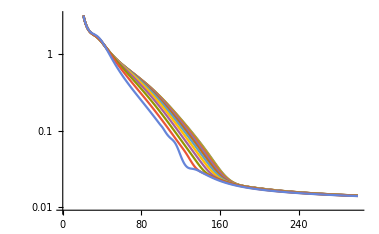

```mathematica
ListLinePlot[Table[Transpose[{T,c2data[[i]]}],{i,1,Length[mub]}],ScalingFunctions->"Log"]
```

### Freeze-out line

```mathematica
STARFitI=Transpose[{Flatten[Import["./freezeout/mub.dat"]],Flatten[Import["./freezeout/STARFitI.dat"]]}];
STARFitII=Transpose[{Flatten[Import["./freezeout/mub.dat"]],Flatten[Import["./freezeout/STARFitII.dat"]]}];
TI=Table[Interpolation[STARFitI][mub[[i]]],{i,2,Length[mub]}];
TII=Table[Interpolation[STARFitII][mub[[i]]],{i,2,Length[mub]}];
c2foI=Table[{sqrts[mub[[i]]],(intfun[[i]][TI[[i-1]]])/((*TI[[i-1]]*)1)},{i,2,Length[mub]}];
c2foII=Table[{sqrts[mub[[i]]],(intfun[[i]][TII[[i-1]]])/((*TII[[i-1]]*)1)},{i,2,Length[mub]}];
```

```mathematica
mubfo[sqrts_]:=1307.5/(1+0.288 sqrts);
sqrts[muB_]:=-(1.7361111111111112 (-2615.+2. muB))/muB;
Tfo[muB_]:=158.4/(1+Exp[2.60-Log[(1307.5/muB-1)/0.288]/0.45]);
```

```mathematica
sqrts[mub[[2;;-1]]]
```

{87.3264,41.9271,26.794,19.2274,14.6875,11.6609,9.49901,7.8776,6.61651,5.60764,4.7822}

```mathematica
Tfo[mub[[2;;-1]]]
```

{158.296,157.873,156.982,155.465,153.139,149.806,145.257,139.296,131.77,122.612,111.88}

```mathematica
data=Table[Transpose[{T,c2data[[i]]/3}],{i,1,Length[mub]}];
intfun=Table[Interpolation[data[[i]]],{i,1,Length[mub]}];
c2fo=Table[{sqrts[mub[[i]]],intfun[[i]][Tfo[mub[[i]]]-0]},{i,2,Length[mub]}];
```

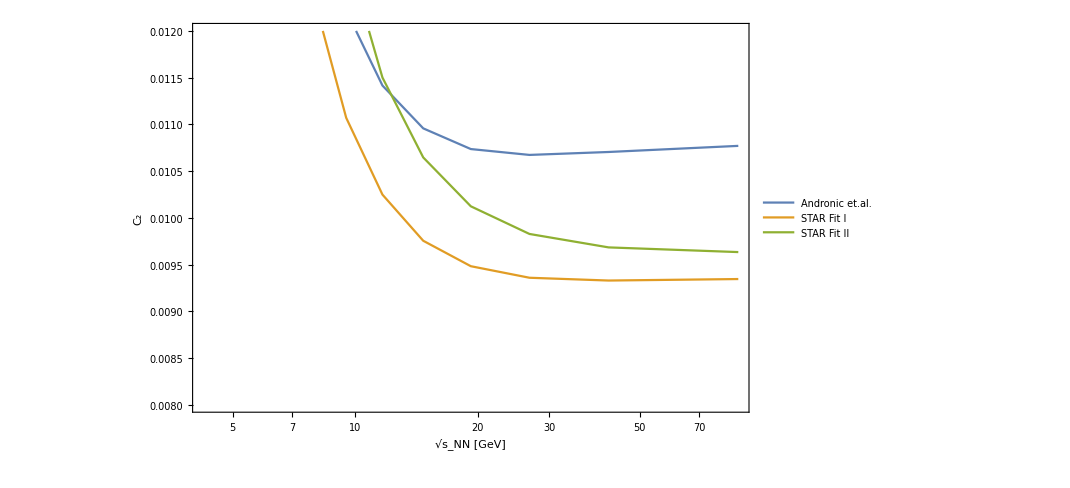

```mathematica
ListLinePlot[{c2fo,c2foI,c2foII},PlotRange->{All,{0.008,0.012}},ScalingFunctions->{"Log",Automatic},PlotLegends->{"Andronic et.al.","STAR Fit I","STAR Fit II"},Frame->True,FrameLabel->{Style["√s_NN [GeV]",Black,15,FontFamily->"Times New Roman"],Style["C_2",Black,15,FontFamily->"Times New Roman"]}]
```